```mathematica
xdata={-15,-11,-7,-3,1,5,9,13,17,21,25,29,33,37,41};
ydata={0.47,0.54,0.79,1.32,1.13,1.26,3.02,2.99,3.15,3.90,5.04,7.72,11.02,13.42,20.85};
```

```mathematica
Grid[Transpose[{xdata,ydata}]]
```

-15 | 0.47
-11 | 0.54
-7 | 0.79
-3 | 1.32
1 | 1.13
5 | 1.26
9 | 3.02
13 | 2.99
17 | 3.15
21 | 3.9
25 | 5.04
29 | 7.72
33 | 11.02
37 | 13.42
41 | 20.85

```mathematica
Grid[Transpose[{xdata,ydata}]]//TeXForm//CopyToClipboard
```

```mathematica
xbar=Mean[xdata]
ybar=Mean[ydata]
```

13

5.108

```mathematica
Length[xdata]
```

15

```mathematica
σTρ=Sum[(xdata[[i]]-xbar)(ydata[[i]]-ybar),{i,1,Length[xdata]}]/Length[xdata]
```

83.688

```mathematica
σT=Sqrt[Sum[(xdata[[i]]-xbar)^2,{i,1,Length[xdata]}]/Length[xdata]]//N
```

17.282

```mathematica
σρ=Sqrt[Sum[(ydata[[i]]-ybar)^2,{i,1,Length[xdata]}]/Length[xdata]]//N
```

5.6499

```mathematica
σTρ/(σT σρ)
```

0.857095

```mathematica
LinearModelFit[Transpose[{xdata,ydata}],x,x]["RSquared"]//Sqrt
```

0.857095

```mathematica
%35["CovarianceMatrix"]
```

{{1.0204,-0.0283646},{-0.0283646,0.00218189}}

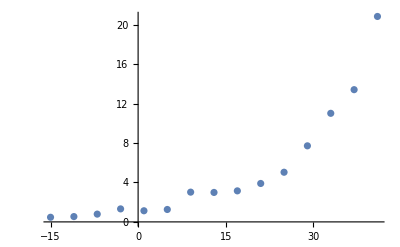

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```